# CCBH coupling and Power Law + Peak

Davi  C. Rodrigues (this code). May, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled Black Hole (arbitrary k value)
DEBH = Dark Energy coupled Black Hole (implies k = - 3w)
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
(* 
  DIRECTORY STRUCTURE
  *******************
*)

pathBase = NotebookDirectory[];
pathOut = FileNameJoin[{pathBase, "output"}];
pathIn =  FileNameJoin[{pathBase, "input"}];
pathAux = FileNameJoin[{pathBase, "auxiliary"}];

exportOut[fileName_, variable_] := (
  Export[FileNameJoin[{pathOut, fileName}], variable];
  "pathOut/"<>fileName
);
exportAux[fileName_, variable_] := (
  Export[FileNameJoin[{pathAux, fileName}], variable];
  "pathAux/"<>fileName
);
SetAttributes[dumpsave, HoldRest];
dumpsave[fileName_, variable_] := (
  DumpSave[FileNameJoin[{pathAux, fileName}], variable];
  "pathAux/"<>fileName
);
getAux[fileName_] := Get[FileNameJoin[{pathAux, fileName}]];

SetDirectory[pathBase];

(*
  PHYSICAL CONSTANTS
  ******************
*)

(*ΩΛ = 0.6889;*) (*2018 data from Planck*)
(*Ωm = 0.315; (*2018 data from Planck*)
H0Gy = 67.66 / (kpc 10^3) gyr; (*1/Gyr, 2018 data from Planck, 67.66 km/s Mpc^-1*)
*)
Ωm = 0.32;
H0Gy = 70.0 / (kpc 10^3) gyr; (* With these rounded values, the universe age is 13.2 GY*)
gyr = 10^9 60 60 24 365; (*Gyr in seconds*)
kpc = 3.08568 10^16; (*kpc in km*)

(* ------ *)
w0 = -1; (*w0 is the standard value for w, the DE equation of state parameter*)
k0 = 3; (*k0 is the standard growth exponent for CBH.*)
tdmax0 = 13.0; (*Gyrs. The standard maximum delay time. 
13.5 Gyrs from GWTC-3 2111.03634v4 (population paper), but we adopt here a slightly smaller value*)
tdmin0 = 0.05; (*Gyrs. The standard minimum delay time. From GWTC-3 population paper*)
zMax0 = 10; (* Highest redshift where BBH start to form. In accordance with GWTC-3, arXiv:2111.03634v4 (population paper) *)


(*
  META PARAMETERS AND OPTIONS
  ****************************
*)
baseSimPoints = 10^6; (*The base number of points to be simmulated for each dimension. 
  10^6 is satisfatory and fast, 10^7 is publication version.*)
optionstkw = {
  tdmin -> tdmin0, 
  tdmax -> tdmax0, 
  k -> k0, 
  w -> w0, 
  zMax -> zMax0
};


(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

findSigma::usage = "findSigma[probability] yields the number of σ's for a given probability.";
findSigma[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];


(*
  Calling wl files
  ***************** 
*)

<<"GWTC-3-DataPreparation.wl" 

(* exportOut["plotZxM.pdf", plotZxM] *)

<<"PowerLawPlusPeakDefinition.wl"
```

Event that is in gwPopEvents, but not in gwtcEvents (pos200105):   54

Event that is in gwPopEvents, but not in gwtcEvents (pos190426):   69

datasetGWpop lines to be neglected:   {{9},{16},{54},{69}}

Number of m1 black holes:   72

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

## Mass factor correction (massFactor)

### Defining cosmology and BBH parameters

```mathematica
Clear[zFormation, hubble, timeZ, w, z];

hubble[z_, w_] = H0Gy Sqrt[Ωm(1+z)^3+(1-Ωm)(1+z)^(3(1+w))]; 

Clear[timeZ];
timeZ[z1_?NumberQ, z2_?NumberQ, w_] := NIntegrate[
  ((1+z) hubble[z, w])^-1, 
  {z, z1, z2}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0}, (*Improves computational time by a factor 5-10, without changes in the answers.*)
  PrecisionGoal -> 5,
  AccuracyGoal -> Infinity,
  MaxRecursion -> 10  (*Removing this may improve speed, it is necessary to check*)
];

zFormation[zObs_?NumberQ, delayTime_?NumberQ, zMax_, w_] := If[
  timeZ[zObs, zMax, w] > delayTime, (*Time between zObs and zMax > td*)
  (*then*)
  FindRoot[
    timeZ[zObs, zformation, w] == delayTime, 
    {zformation, zObs, zMax}, 
    PrecisionGoal -> 5, (*Reminder: AccuracyGoal behaves differently in FindRoot. This is just a minimum precision requirement, probably it will be higher.*)
    Method -> "Brent" (*This is the automatic method for this case, but I am stating it explicitly.*)
  ][[1,2]],
  (*else*)
  zMax  
];

listDelayTime = Range[tdmin0/10, tdmax0, 0.015]; (* delayTime values to be computed. tdmin lower than tdmin0 will be considered*)
listzObs = Range[0.0, 1.0, 0.01];
listw = Range[-1.5, -0.5, 0.1]; 

Clear[minDelayTime, maxDelayTime];
minDelayTime = First[listDelayTime]; (*min delay time to be computed, it can be lower than tdmin0*)
maxDelayTime[zObs_, tdmax_?NumberQ, zMax_?NumberQ, w_] := maxDelayTime[zObs, tdmax, zMax, w] = Min[
  tdmax,
  (*Select[listDelayTime, # <=  tdmax &] // Last, (*essentially, this is the same of tdmax, but it picks a given element of listDelayTime*)*)
  timeZ[zObs, zMax, w]
]; 

massFactor[zObs_,zFormation_, k_] = ((1 + zFormation)/(1 + zObs))^k; (*(a/Subscript[a, i])^k. This is the factor that corrects the mass*)
```

Verifying universe age and the time between z = 10  and today.

```mathematica
Round[timeZ[0, 10^6, w0], 0.1]
timeZ[0,10, w0]
```

13.8

13.2819

```mathematica
maxDelayTime[0.05, tdmax0, zMax0, w0]
```

12.5847

For zMax = 10, the upper limit on t_d < 13.5 Gyrs is useless, since z = 10 corresponds to 13.28 Gyrs.

### Defining zFormationI from a set of computed points.

```mathematica
isComputeTableZformation = False; (*Change to True to compute and regenerate the mx file. About 10 min.*)

If[isComputeTableZformation, 
  Echo["Computing tableZformation..."];
  tableZformation = ParallelTable[
    {{zObs, delayTime, w1}, zFormation[zObs, delayTime, zMax0, w1]}, (*this table uses zMax0, zFornationI can restrict that*)
    {zObs, listzObs},
    {delayTime, listDelayTime}, (*It is computed up to tdmax0*)
    {w1, listw}
  ]; // EchoTiming;
  tableZformationFlat = Flatten[tableZformation, 2];
  dumpsave["tableZformation.mx", tableZformationFlat],
  (*else*)
  getAux["tableZformation.mx"];
  Echo["tableZformation loaded."];
];

Clear[zFormationIraw, zFormationIfast, zFormationI]
zFormationInoZmax[zObs_, delayTime_, w_] = Interpolation[
  tableZformationFlat,
  InterpolationOrder -> 1 
][zObs, delayTime, w]; (*the "I" in the name stands for interpolated. "raw" for no options.*)

(*zFormationIfast[zObs_, delayTime_, opts:OptionsPattern[optionstkw]] = zFormationIraw[zObs, delayTime, OptionValue@w]; *)
(*the "fast" version does not implement the zMax option, thus zMax = zMax0, about 2-3 times faster*)

SetAttributes[zFormationI, Listable]; (*zFormationInoZmax is automatically listable, but the Min function is not Listable*)
zFormationI[zObs_, delayTime_, zMax_, w_] = Min[
  zFormationInoZmax[zObs, delayTime, w],
  zMax
];
```

tableZformation loaded.

Sending zFormationI to the subkernels.

Does not work well. All my tries to parallelize any computation that depends on zFormationI were not successful: interpolating functions in the subkernels are slower than in the kernel.

```mathematica
(*DistributeDefinitions[tableZformationFlat]; (*Takes several seconds.*)
Echo["Distributed."];
ParallelEvaluate[
  zFormationInoZmax[zObs_, delayTime_, w_] = Interpolation[
    tableZformationFlat,
    InterpolationOrder -> 1 
  ][zObs, delayTime, w]
]; (*Takes several seconds*)

ParallelEvaluate[
  SetAttributes[zFormationI, Listable]; (*zFormationInoZmax is automatically listable, but the Min function is not Listable*)
  zFormationI[zObs_, delayTime_, zMax_, w_] = Min[
    zFormationInoZmax[zObs, delayTime, w],
    zMax
  ];
]; (*Quick*)
*)
```

Distributed.

#### Verifying the interpolation

Inspecting the computed points and the interpolation

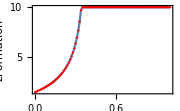
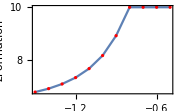
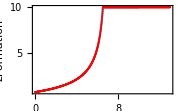
Visually checking the interpolation:   -Graphics--Graphics--Graphics-

```mathematica
originalPlotOptions = Options[Plot];
SetOptions[Plot, Frame -> True, Axes -> False, PlotRange -> All];

Echo[
  Row[{
    Show[
      Plot[zFormationI[zObs, 9, zMax0, w0], 
        {zObs, 0.05, 1.0}, 
        FrameLabel->{"zObs", "zFormation"}
      ], 
      ListPlot[{#, zFormation[#, 9, zMax0, w0]} & /@ listzObs, PlotStyle->Red],
      ImageSize -> Small
    ],
    Show[
      Plot[zFormationI[1, 5, zMax0, w1], 
        {w1, -1.5, -0.5}, 
        FrameLabel->{"w", "zFormation"}
      ], 
      ListPlot[{#, zFormation[1, 5, zMax0, #]} & /@ listw, PlotStyle->Red],
      ImageSize -> Small
    ],
    Show[
      Plot[zFormationI[0.7, delayTime, zMax0, w0], 
        {delayTime, 0.1, 10}, 
        FrameLabel->{"t_d", "zFormation"}
      ], 
      ListPlot[{#, zFormation[0.7, #, zMax0, w0]} & /@ listDelayTime, PlotStyle->Red],
      ImageSize -> Small
    ]
  }],
  "Visually checking the interpolation: "
];
SetOptions[Plot, originalPlotOptions];
```

### The mass factor distribution (𝒟MassFactor & 𝒟InvMassFactor)

ATTENTION: 𝒟MassFactor and dataMassFactor do not work well under paralelization. This is a known issue with computing interpolated function in parallel, and they depend on zFormationI. If zFormatino is used in place, the parallelization works fine, but the improvement of using zFormationI is a factor of ~100, thus parallelizing is not worth. To avoid the issue, I tried doing the interpolatin in the subkernels, but there was no relevant improvement. So I stopped trying to parallel these functions.

```mathematica
ClearAll[
  𝒟MassFactor,
  massFactorDelay, 
  dataMassFactor,
  𝒟InvMassFactor,
  dataDelayTime
];

SetAttributes[massFactorDelay, Listable];
massFactorDelay[zObs_, delayTime_, k_, zMax_, w_] =  massFactor[zObs, zFormationI[zObs, delayTime, zMax, w], k];

randomLogDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_, realizations_] := randomLogDelayTime[zObs, tdmin, tdmax,  zMax, w, realizations] = 
 RandomReal[{Log10[tdmin], Log10 @ maxDelayTime[zObs, tdmax, zMax, w]}, realizations]; (*log-flat distribution.*)
 
proportionalBaseSimPoints[tdmin_, tdmax_] = Min[Round[(tdmax - tdmin)/(tdmax0 - tdmin0) 2 baseSimPoints], 2 baseSimPoints]; (*The maximum number of realizations is 2 baseSimPoints, 
but this number can get smaller proportionally to tdmax - tdmin. *)

dataDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_] := dataDelayTime[zObs, tdmin, tdmax, zMax, w] = 
 10^randomLogDelayTime[zObs, tdmin, tdmax, zMax, w,  proportionalBaseSimPoints[tdmin, tdmax]]; 

dataMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := dataMassFactor[zObs, tdmin, tdmax, k, zMax, w] = 
 massFactorDelay[zObs, dataDelayTime[zObs, tdmin, tdmax, zMax, w], k, zMax, w];
 
𝒟MassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟MassFactor[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataMassFactor[zObs, tdmin, tdmax, k, zMax, w], 
  0.001 (*Manual selection of the band, leads to 0.1% maximum mass precision. Silverman leads to 0.06 for the bandwidth, SheaterJones takes a lot of time and does not converge.*), 
  InterpolationPoints -> 10^4, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
];

𝒟InvMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟InvMassFactor[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  1/dataMassFactor[zObs, tdmin, tdmax, k, zMax, w], 
  0.001 (*Manual selection of the band, leads to 0.1% maximum mass precision. Silverman leads to 0.06 for the bandwidth, SheaterJones takes a lot of time and does not converge.*), 
  InterpolationPoints -> 10^4, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
];
```

#### 𝒟InvMassFactor plot

```mathematica
isCompute𝒟MassFactorCases = False; (*Saved with 2 10^6 realizations*) 

If[isCompute𝒟MassFactorCases, 
  Echo["Computing 𝒟MassFactor 0.05 and 0.9 cases..."];
  𝒟InvMassFactor005 = 𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0]; // EchoTiming;
  𝒟InvMassFactor09 = 𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0]; // EchoTiming; (*Issue: parallelizing here has several issues, it is quicker this way.*)
  dumpsave["DInvMassFactor005.mx", 𝒟InvMassFactor005];
  dumpsave["DInvMassFactor09.mx", 𝒟InvMassFactor09],
  (*else*)
  getAux["DInvMassFactor005.mx"];
  getAux["DInvMassFactor09.mx"];
  𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0] = 𝒟InvMassFactor005;
  𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0] = 𝒟InvMassFactor09;
  Echo["𝒟MassFactor 0.05 and 0.9 cases loaded."];
];
```

Computing 𝒟MassFactor 0.05 and 0.9 cases...

0.017047

0.061061

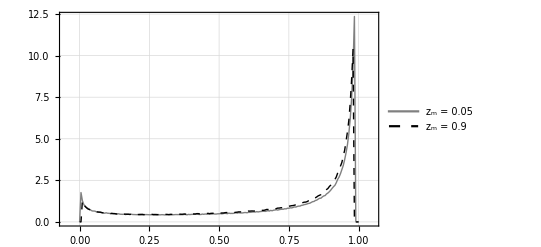

pathOut/plotInverseMassFactorDistribution.pdf

```mathematica
plotInverseMassFactorDistribution = Block[{pdfValues1, pdfValues2},
  pdfValues1 = {#, PDF[𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.005];
  pdfValues2 = {#, PDF[𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.005];
  ListPlot[
    {pdfValues1, pdfValues2}, 
    Joined -> True, 
    PlotRange -> {{-0.05,1.05}, All},
    Frame-> True,
    Axes -> False,
    Background->White,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    PlotStyle-> {{Thick, Gray}, {Thick, Dashed, Black}},
    PlotLegends -> Placed[{
      Style["z_m = 0.05", FontFamily->"Times", FontSize -> 15], 
      Style["z_m = 0.9", FontFamily->"Times", FontSize -> 15]},
      {0.2, 0.75}
    ],
    GridLines->Automatic,
    GridLinesStyle->Directive[Dotted, Gray]
  ]
]

exportOut["plotInverseMassFactorDistribution.pdf", plotInverseMassFactorDistribution]
```

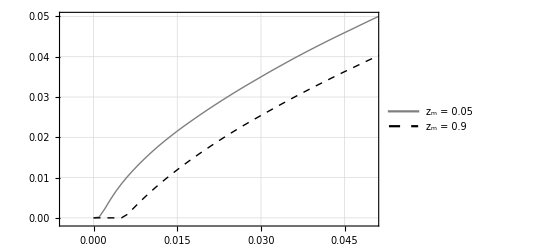

pathOut/plotInverseMassFactorCDF.pdf

```mathematica
plotInverseMassFactorCDF = Block[{cdfValues1, cdfValues2},
  cdfValues1 = {#, CDF[𝒟InvMassFactor[0.05, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.001];
  cdfValues2 = {#, CDF[𝒟InvMassFactor[0.9, tdmin0, tdmax0, k0, zMax0, w0], #]} & /@ Range[0,1,0.001];
  ListPlot[
    {cdfValues1, cdfValues2}, 
    Joined -> True, 
    PlotRange -> {{-0.005,0.05}, {-0.001, 0.05}},
    Frame-> True,
    Axes -> False,
    Background->White,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    PlotStyle-> {{Thick, Gray}, {Thick, Dashed, Black}},
    PlotLegends -> Placed[{
      Style["z_m = 0.05", FontFamily->"Times", FontSize -> 15], 
      Style["z_m = 0.9", FontFamily->"Times", FontSize -> 15]},
      {0.2, 0.75}
    ],
    GridLines->Automatic,
    GridLinesStyle->Directive[Dotted, Gray]
  ]
]

exportOut["plotInverseMassFactorCDF.pdf", plotInverseMassFactorCDF]
```

## Formation mass distribution

```mathematica
ClearAll[
  dataM1Formation, dataM1FormationRaw,
  𝒟M1Formation, 𝒟M1FormationRaw,
  dataM1Merger
];

𝒟plp = plpp`𝒟[]; (*To use other PLPP parameter values, change here, e.g. 𝒟plp = plpp`𝒟[plpp`dm -> 9];*)
dataM1Merger = RandomVariate[𝒟plp, 2 baseSimPoints] ~ EchoTiming ~ "dataM1Merger";
dataM1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_]:= dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]= Block[
  {length, dataM1MergerSameLength},
  length = Length @ dataMassFactor[zObs, tdmin, tdmax, k, zMax, w];
  dataM1MergerSameLength = Take[dataM1Merger, length];
  1/dataMassFactor[zObs, tdmin, tdmax, 1, zMax, w]^k dataM1MergerSameLength 
];(*Note that the k=1 inside dataMassFactor, but there is k in the exponent. It's relevant for function memmory, 
such that dataMassFactor needs not to be comptuted again if k changes.*)

dataM1Formation[zObs_, opts:OptionsPattern[optionstkw]] := dataM1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
]

𝒟M1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M1FormationRaw[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w],
  0.1, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
];

𝒟M1Formation[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];
```

"dataM1Merger"  4.84329

```mathematica
dataM1Formation[0.4]; //EchoTiming
dataM1Formation[0.4, k-> 0.5]; //EchoTiming
histFormation3 = Histogram[
  {dataM1Formation[0.4], dataM1Formation[0.4, k-> 0.5], dataM1Merger}, 
  {.2}, 
  "PDF", 
  PlotRange->{{0,50}, All},
  Background->White,
  ChartStyle->{Lighter@Orange, ColorData["AvocadoColors"][0.5], Lighter@Blue},
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  ChartLegends -> Placed[{
    Style["k = 3.0", FontFamily->"Times", FontSize -> 15], 
    Style["k = 0.5", FontFamily->"Times", FontSize -> 15], 
    Style["k = 0.0", FontFamily->"Times", FontSize -> 15]}, 
    {0.8, 0.75}
  ]
]

(*exportOut["histFormation3.pdf", histFormation3]*)
```

42.8218

22.4644

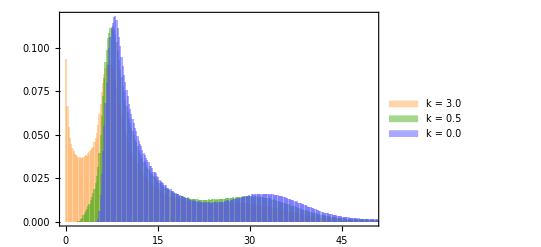

```mathematica
tdmaxE = 5;
tdminE = 0.005;
zMaxE = 2;
𝒟M1Formation[0.4]; //EchoTiming
𝒟M1Formation[0.4, k-> 0.5]; //EchoTiming
𝒟M1Formation[0.4, tdmax -> tdmaxE]; //EchoTiming
𝒟M1Formation[0.4, tdmin -> tdminE]; //EchoTiming
𝒟M1Formation[0.4, zMax -> zMaxE]; //EchoTiming

legend = LineLegend[
  {Lighter@Orange, {Lighter@Orange, Dashed}, {Lighter@Orange, Dotted}, {Lighter@Orange, DotDashed}, ColorData["AvocadoColors"][0.5], Lighter@Blue}, 
  {
    Style["k=3.0", FontFamily->"Times", FontSize -> 11], 
    Style["k=3.0, t_max=" <> ToString[Round@tdmaxE]<>" Gyr", FontFamily->"Times", FontSize -> 11], 
    Style["k=3.0, t_min=" <> ToString[Round[10^3 tdminE]]<>" Myr", FontFamily->"Times", FontSize -> 11],
    Style["k=3.0, z_max=" <> ToString[Round[zMaxE]], FontFamily->"Times", FontSize -> 11],
    Style["k=0.5", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.0", FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 14, 
  Spacings -> 0.15 (*It works, although in red*)
];
Off[General::munfl]; 
plotPDFformationDist = LogLogPlot[
  {
    PDF[𝒟M1Formation[0.4], x], 
    PDF[𝒟M1Formation[0.4, tdmax -> tdmaxE], x], 
    PDF[𝒟M1Formation[0.4, tdmin -> tdminE], x], 
    PDF[𝒟M1Formation[0.4, zMax -> zMaxE], x],
    PDF[𝒟M1Formation[0.4, k-> 0.5], x], 
    PDF[𝒟plp, x]
  }, 
  {x, 0.5, plpp`mMax /. optionsPlpp}, 
  PlotRange->{{0.5, 400}, { 3 10^-4, .3}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{
    {Thick, Lighter@Orange}, 
    {Thick, Lighter@Orange, Dashed}, 
    {Thick, Lighter@Orange, Dotted}, 
    {Thick, Lighter@Orange, DotDashed}, 
    {Thick, ColorData["AvocadoColors"][0.5]}, 
    {Thick, Lighter@Blue}},
  PlotLegends-> Placed[legend, {0.82,0.71}]
]
On[General::munfl];

exportOut["plotPDFformationDist.pdf", plotPDFformationDist]
```

0.000015

0.000015

0.000015

0.000016

0.000017

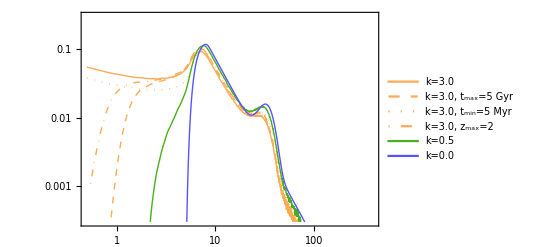

pathOut/plotPDFformationDist.pdf

## Probabilities for 2<m_th<5

m_th is the threshold mass.

### Computing the relevant distributions

Before the applications, Loading or computing the relevant distributions,

```mathematica
listZobs = (mXzDataForPlotting1 /. Around[x_, y_] -> x)[[All,1]] // Sort;

isComputeTable𝒟M1FormationAllZobs = False; (*Change to True to compute and regenerate the mx file. About 15 min.*)

If[isComputeTable𝒟M1FormationAllZobs, 
  Echo["Computing table𝒟M1FormationAllZobs..."];
  tableDM1FormationAllZobs = Table[
    {zObs, 𝒟M1Formation[zObs]}, 
    {zObs, DeleteDuplicates[listZobs]}
  ]; // EchoTiming;
  dumpsave["tableDM1FormationAllZobs.mx", tableDM1FormationAllZobs],
  (*else*)
  getAux["tableDM1FormationAllZobs.mx"];
  (𝒟M1Formation[#1] = #2) & @@@ tableDM1FormationAllZobs;
  Echo["tableDM1FormationAllZobs loaded."];
];
```

tableDM1FormationAllZobs loaded.

### Probabilities related with minimum mass from the above distributions

```mathematica
Clear[listProb, listProbRaw, probabilityMmin, probabilityMminApprox];
listProbRaw[mMin_, tdmin_, tdmax_, k_, zMax_, w_] := listProbRaw[mMin, tdmin, tdmax, k, zMax, w] = 
 NProbability[x>mMin, x \[Distributed] 𝒟M1FormationRaw[#, tdmin, tdmax, k, zMax, w]] & /@  listZobs;
listProb[mMin_, opts:OptionsPattern[optionstkw]] :=  listProbRaw[mMin, OptionValue @ tdmin, OptionValue @ tdmax, OptionValue @ k, OptionValue @ zMax, OptionValue @ w];

probabilityMmin[mMin_, opts:OptionsPattern[optionstkw]] :=  Times @@ listProb[mMin, opts];
probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := NProbability[x>mMin, x \[Distributed] 𝒟M1Formation[0.4, opts]]^72;

Echo[{probabilityMmin[2], findSigma[probabilityMmin[2]]}, "Probability that the model is correct and the sigma level of rejection: "];
Echo[{probabilityMminApprox[2], findSigma[probabilityMminApprox[2]]}, "Same as above, for the approximation case: "];
```

Probability that the model is correct and the sigma level of rejection:   {0.00058694,3.43758}

Same as above, for the approximation case:   {0.000659773,3.40577}

Hence, with m_th = 2, the standard CCBH with k =3 is explided at more than 3 σ. Note that the approximation is quite good.

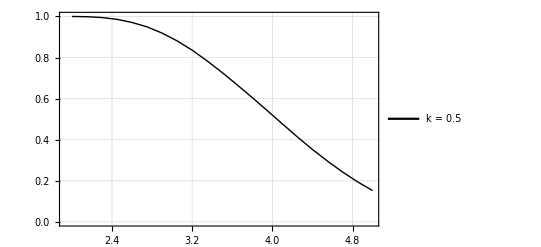

pathOut/plotProbabiliyNull005.pdf

```mathematica
out1 = NProbability[Abs[x] > 1, x\[Distributed]NormalDistribution[]];
out2 = NProbability[Abs[x] > 2, x\[Distributed]NormalDistribution[]];
out3 = NProbability[Abs[x] > 3, x\[Distributed]NormalDistribution[]];
out4 = NProbability[Abs[x] > 4, x\[Distributed]NormalDistribution[]];
out5 = NProbability[Abs[x] > 5, x\[Distributed]NormalDistribution[]];

plotProbabiliyNull005 = Block[
  {list = {#, probabilityMminApprox[#, k-> 0.5] } & /@ Range[2,5,0.15]},
  ListPlot[list, 
    Joined->True,
    PlotStyle->{Thick, Black},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{Automatic, {{out1, "1σ"}, {out2, "2σ"}}}, {Automatic, Automatic}},
    GridLines->Automatic,
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[{Style["k = 0.5", FontFamily->"Times", FontSize -> 14], Style["k = 1.0", FontFamily->"Times", FontSize -> 14]}, {0.8,0.8}]
  ]
]

exportOut["plotProbabiliyNull005.pdf", plotProbabiliyNull005]
```

```mathematica
list1 = {#, probabilityMminApprox[#]} & /@ Range[2,5,0.5];
list2 = {#, probabilityMminApprox[#, k-> 3 0.9 , w-> -0.9]} & /@ Range[2,5,0.5];
list3 = {#, probabilityMminApprox[#, k-> 3 1.1 , w-> -1.1 ]} & /@ Range[2,5,0.5];
list4 = {#, probabilityMminApprox[#, k-> 3 0.7 , w-> -0.7]} & /@ Range[2,5,0.5];
list5 = {#, probabilityMminApprox[#, k-> 3 1.3 , w-> -1.3 ]} & /@ Range[2,5,0.5];
```

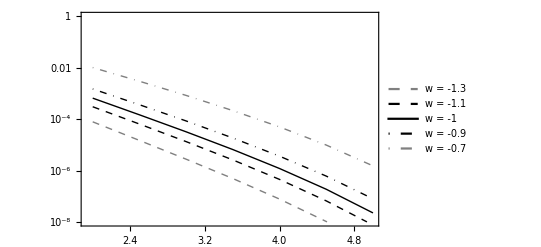

pathOut/plotProbabilityNullw.pdf

```mathematica
plotProbabilityNullw = Block[
  {numbers},
  numbers = Table[{10^-i, StringReplace["10^-a", "a" -> ToString[i]]}, {i, 1, 8, 2}];
  ListLogPlot[{list5, list3, list1, list2, list4}, 
    Joined->True,
    PlotStyle->{{Thick, Dashed, Gray}, {Thick, Dashed, Black}, {Thick, Black}, {Thick, DotDashed, Black}, {Thick, DotDashed, Gray}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{numbers, {{out1, "1σ"}, {out2, "2σ"}, {out3, "3σ"}, {out4, "4σ"}, {out5, "5σ"}}}, {Automatic, Automatic}},
    PlotRange->{All, {10^-8,  1}},
    GridLines->Automatic,
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[
      {
        Style["w = -1.3", FontFamily->"Times", FontSize -> 12],
        Style["w = -1.1", FontFamily->"Times", FontSize -> 12], 
        Style["w = -1", FontFamily->"Times", FontSize -> 12], 
        Style["w = -0.9", FontFamily->"Times", FontSize -> 12], 
        Style["w = -0.7", FontFamily->"Times", FontSize -> 12]        
      },
      {0.8,0.75}
    ]
  ]
]

exportOut["plotProbabilityNullw.pdf", plotProbabilityNullw]
```

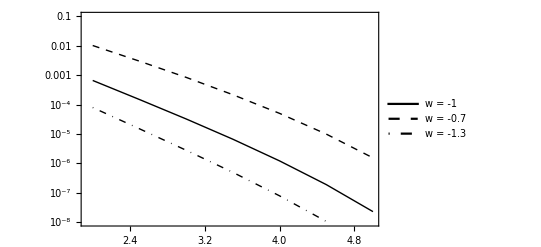

```mathematica
(*plotProbabilityNullw = Block[
  {
    list1 = {#, probabilityMminApprox[#]} & /@ Range[2,5,0.5],
    list2 = {#, probabilityMminApprox[#, k-> 3 0.7 , w-> -0.7]} & /@ Range[2,5,0.5],
    list3 = {#, probabilityMminApprox[#, k-> 3 1.3 , w-> -1.3 ]} & /@ Range[2,5,0.5]
  },
  ListLogPlot[{list1, list2, list3}, 
    Joined->True,
    PlotStyle->{{Thick, Black}, {Thick, Dashed, Black}, {Thick, DotDashed, Black}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{Automatic, {{out1, "1σ"}, {out2, "2σ"}, {out3, "3σ"}, {out4, "4σ"}, {out5, "5σ"}}}, {Automatic, Automatic}},
    PlotRange->{All, {10^-8,  0.1}},
    GridLines->Automatic,
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[{
      Style["w = -1", FontFamily->"Times", FontSize -> 14], 
      Style["w = -0.7", FontFamily->"Times", FontSize -> 14], 
      Style["w = -1.3", FontFamily->"Times", FontSize -> 14]},
      {0.8,0.8}
    ]
  ]
]

(*exportOut["plotProbabilityNullw.pdf", plotProbabilityNullw]*)
*)
```

## Confidence plots with variable, k, tdmax, tdmin, zMax...

```mathematica
isComputeTable𝒟M1Formation = True; (*Change to True to compute and regenerate the mx file. About 2-3 min.*)

(*kValues = Range[0.2, 3, 0.2];
tValues = Range[tdmax0/5, tdmax0, tdmax0/20];*)

kValues = Range[0.25, 3, 0.25];
tValues = Range[tdmax0/5, tdmax0, tdmax0/10];

If[isComputeTable𝒟M1Formation, 
  Echo["Computing table𝒟M1Formation..."];
  table𝒟M1Formation = Table[
    𝒟M1Formation[0.4, k-> k1, tdmax-> tdmax1], 
    {k1, kValues}, 
    {tdmax1, tValues}
  ]; // EchoTiming;
  dumpsave["tableDM1Formation.mx", table𝒟M1Formation],
  (*else*)
  getAux["tableDM1Formation.mx"];
  Echo["table𝒟M1Formation loaded."];
];
```

Computing table𝒟M1Formation...

```mathematica
k1
```

0.8

```mathematica
𝒟M1Formation[0.4, k-> 0.2, tdmax-> tdmax0/5]
```

DataDistribution[<<SmoothKernel>>, {2000000}]

```mathematica
tdmax1
```

3.9

```mathematica
dumpsave["tableDM1FormationPartial.mx", table𝒟M1Formation]
```

pathAux/tableDM1FormationPartial.mx

```mathematica
isComputeTable𝒟M1FormationW = True; (*Change to True to compute and regenerate the mx file. About 2-3 min.*)

wValues = listw;
tValues = Range[tdmax0/5, tdmax0, tdmax0/20];

If[isComputeTable𝒟M1FormationW, 
  Echo["Computing table𝒟M1FormationW..."];
  table𝒟M1FormationW = ParallelTable[
    𝒟M1Formation[0.4, k-> - 3 w1, w -> w1, tdmax-> tdmax1], 
    {w1, wValues}, 
    {tdmax1, tValues}
  ]; // EchoTiming;
  dumpsave["tableDM1FormationW.mx", table𝒟M1Formation],
  (*else*)
  getAux["tableDM1FormationW.mx"];
  Echo["table𝒟M1FormationW loaded."];
];
```

Computing table𝒟M1FormationW...

275.714

```mathematica
Clear[tableProbabilityKT, probabilityKT];
tableProbabilityKT[minMass_] := tableProbabilityKT[minMass] = Block[
  {probAux},
  probAux[minMass1_, nk1_, nt1_] := NProbability[x>minMass1, x \[Distributed] table𝒟M1Formation[[nk1, nt1]]]^72;
  ParallelTable[
    {{kValues[[nk]], tValues[[nt]]}, probAux[minMass, nk, nt]}, 
    {nk, Length @ kValues}, (*The number of computed k values*)
    {nt, Length @ tValues} (*The same for tdmax *)
  ]
];
probabilityKT[minMass_, k_, tdmax_] := Interpolation[Flatten[tableProbabilityKT[minMass],1], InterpolationOrder->1][k, tdmax]; 

tableProbabilityWT[minMass_] := tableProbabilityWT[minMass] = Block[
  {probAux},
  probAux[minMass1_, nw1_, nt1_] := NProbability[x>minMass1, x \[Distributed] table𝒟M1FormationW[[nw1, nt1]]]^72;
  ParallelTable[
    {{wValues[[nw]], tValues[[nt]]}, probAux[minMass, nw, nt]}, 
    {nw, Length @ wValues}, (*The number of computed w values*)
    {nt, Length @ tValues} (*The same for tdmax *)
  ]
];
probabilityWT[minMass_, w_, tdmax_] := Interpolation[Flatten[tableProbabilityWT[minMass],1], InterpolationOrder->1][w, tdmax];
```

```mathematica
tableProbabilityWT[2];
```

```mathematica
tableProbabilityKT[5];
```

```mathematica
probOut1σ = NProbability[Abs[x]>1, x\[Distributed]NormalDistribution[]]
probOut2σ = NProbability[Abs[x]>2, x\[Distributed]NormalDistribution[]]
probOut3σ = NProbability[Abs[x]>3, x\[Distributed]NormalDistribution[]]
probOut4σ = NProbability[Abs[x]>4, x\[Distributed]NormalDistribution[]]
```

0.317311

0.0455003

0.0026998

0.0000633425

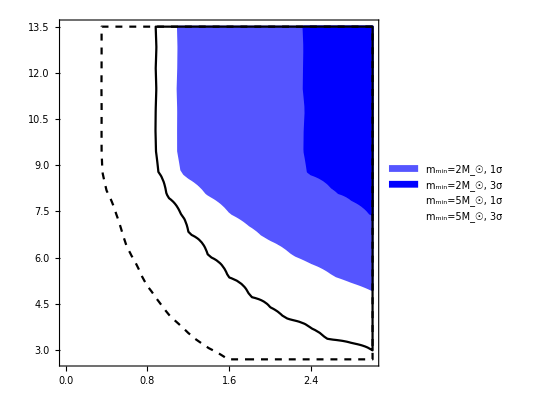

pathOut/plotRegionKT.pdf

```mathematica
plotRegionKT = RegionPlot[
  {
    probabilityKT[2, k,tdmax] < probOut1σ,
    probabilityKT[2, k,tdmax] < probOut3σ,
    probabilityKT[5, k,tdmax] < probOut1σ,
    probabilityKT[5, k,tdmax] < probOut3σ
  },
  {k, .2, 3}, {tdmax, 2.7, 13.5},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Blue], Directive[Blue], None, None},
  BoundaryStyle->{1 -> Directive[Lighter@Blue], 2-> Directive[Blue], 3-> Directive[Black, Dashed],  4-> Directive[Black]},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
  PlotLegends -> Placed[{
    Style["m_min=2M_☉, 1σ", FontFamily->"Times", FontSize -> 12], 
    Style["m_min=2M_☉, 3σ", FontFamily->"Times", FontSize -> 12],
    Style["m_min=5M_☉, 1σ", FontFamily->"Times", FontSize -> 12], 
    Style["m_min=5M_☉, 3σ", FontFamily->"Times", FontSize -> 12]}, 
    {0.15, 0.12}
  ],
  PlotRange->{{0,3}, {2.7, 13.5}}
]

exportOut["plotRegionKT.pdf", plotRegionKT]
```

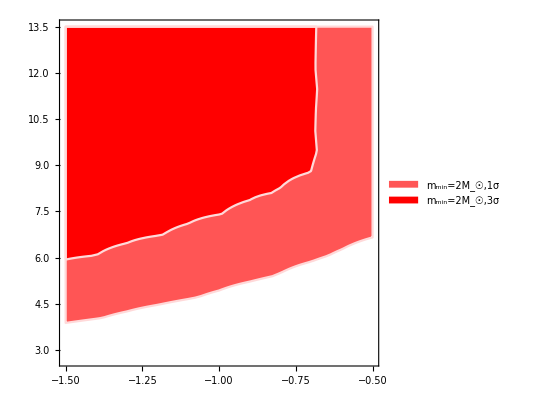

pathOut/plotRegionWT.pdf

```mathematica
plotRegionWT = RegionPlot[
  {
    probabilityWT[2, w,tdmax] < probOut1σ,
    probabilityWT[2, w,tdmax] < probOut3σ
  },
  {w, -1.5, -0.5}, {tdmax, 2.7, 13.5},
  Background->White, 
  PlotStyle-> {Directive[Lighter@Red], Directive[Red]},
  BoundaryStyle->{Red, LightRed},
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotRangePadding->None,
  PlotLegends -> Placed[{
    Style["m_min=2M_☉,1σ", FontFamily->"Times", FontSize -> 15], 
    Style["m_min=2M_☉,3σ", FontFamily->"Times", FontSize -> 15]}, 
    {0.8, 0.10}
  ]
]

exportOut["plotRegionWT.pdf", plotRegionWT]
```

## Plots for the illustration with arrows

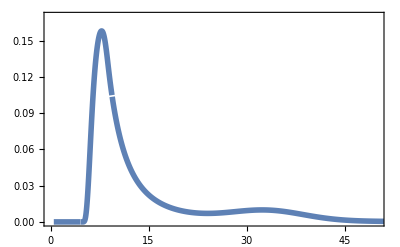

plotArrowsMerger.pdf

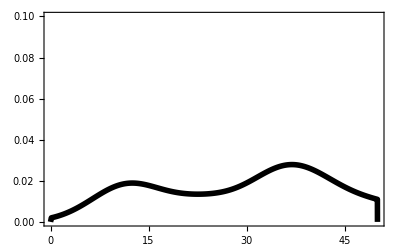

plotArrowsObs.pdf

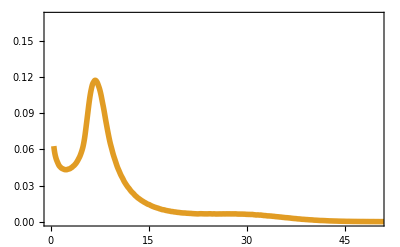

plotArrowsCCBH.pdf

```mathematica
plotArrowsMerger = Plot[
  {PDF[𝒟plp, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,50}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[1]]}}
]

Export["plotArrowsMerger.pdf", plotArrowsMerger]

plotArrowsObs = SmoothHistogram[
  mXzDataForPlotting[[All,2]] /. Around[x_,y_] ->  x, 
  5, 
  "PDF",  
  PlotRange->{{0,50}, {0,.10}}, 
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotStyle->{{Thickness[0.01], Black}}
]

Export["plotArrowsObs.pdf", plotArrowsObs]

plotArrowsCCBH = Plot[
  {PDF[𝒟m1Formationz0403, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,50}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[2]]}}
]

Export["plotArrowsCCBH.pdf", plotArrowsCCBH]
```

## Formation mass distribution straight from observational data

```mathematica
Clear[dataM1ObsFormation];
mXzDataCentralValues = mXzDataForPlotting /. Around[x_, y_] -> x;

dataM1ObsFormation[k_, w_] := dataM1ObsFormation[k, w] =  #2 RandomVariate[𝒟InvMassFactor[#1, k, w], 10^5] &  @@@ mXzDataCentralValues;
```

```mathematica
dataM1ObsFormation[k0, w0] // EchoTiming; (*Check if it indeed has to be so long this computation*)
```

156.571

```mathematica
dataM1ObsFormationk0w0 = dataM1ObsFormation[k0, w0];
DumpSave["dataM1ObsFormationk0w0.mx", dataM1ObsFormationk0w0];
```

```mathematica
dataM1ObsFormation[k0, w0] // EchoTiming;

histFormationDistTest = Histogram[
  dataM1ObsFormation[k0, w0], 
  {0.4}, 
  "PDF", 
  PlotRange->{{0,100}, All},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"]
]
```

3.×10^-6

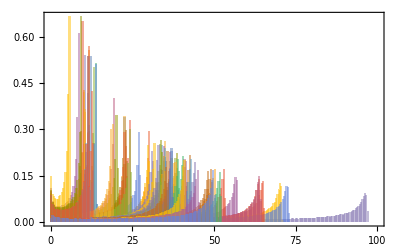

```mathematica
Clear[𝒟M1ObsFormation];
𝒟M1ObsFormation[bhNumber_, k_, w_] := 𝒟M1ObsFormation[bhNumber, k, w] = SmoothKernelDistribution[
  dataM1ObsFormation[k, w][[bhNumber]],
  0.1, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
]
```

```mathematica
𝒟M1ObsFormation[#, k0, w0] & /@ Range[72] // EchoTiming;
```

24.3162

```mathematica
PDF[𝒟M1ObsFormation[1, k0, w0], 20]
```

0.0142567

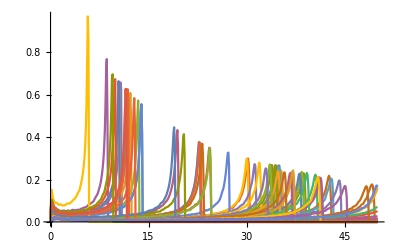

```mathematica
Block[
  {list = Table[{#, PDF[𝒟M1ObsFormation[i, k0, w0], #]} & /@ Range[0, 50, 0.1], {i,72}]},
  ListPlot[list, Joined->True, PlotRange->All]
]
```

```mathematica
probabilityGoodMass[bhNumber_, minimumMass_] := NProbability[m1 > minimumMass, m1 \[Distributed] 𝒟M1ObsFormation[bhNumber, k0, w0]];

totalProbabilityGoodMass[minimumMass_] := Product[probabilityGoodMass[bhNumber, minimumMass], {bhNumber, 1, 72}];
```

```mathematica
totalProbabilityGoodMass[2]
```

0.0101338

```mathematica
FindRoot[NProbability[Abs[x] > x0, x\[Distributed]NormalDistribution[]]==0.01 , {x0 , 2}]
```

{x0→2.57583}